Two lens telescope imaging a focal spot from tilted parabolic mirror. Data from “D:\Public\QuantumNetwork\Zemax\high na design\achromatic lens + mirror\parabolic_0.65na_mirror_edmund_doublet\parabolic + edmund 9mm 25f tilt test + fold mirror + microscope.zmx”

```mathematica
SetDirectory[NotebookDirectory[]];
img=Import["huygens_psf_two_lens_telescope_pt05_deg_mirror_tilt_20220713.bmp"]
data=ImageData[img][[;;,;;,1]];
```

-Graphics-

```mathematica
data
```

{1}
 |  |  |  |

```mathematica
Dimensions[data]
```

{455,606}

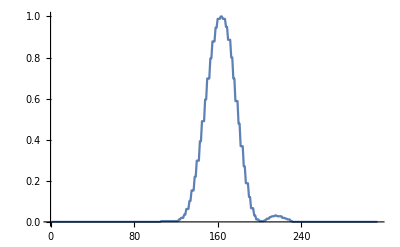

```mathematica
ListPlot[1-data[[26;;338,244]],PlotRange->All,Joined->True]
```